```mathematica
SetDirectory @ NotebookDirectory[];
```

```mathematica
trotterdata = Get["recomp_trotter_fids_3_to_13.txt"]["trotterfids"];
recompdata = Join[
	Get["recomp_trotter_fids_3_to_13.txt"]["recompfids"],
	Get["recomp_fids_from_14_(BACKUP).txt"]["recompfids"]⟦;;8⟧];
```

```mathematica
{trotmin,trotmean,trotmax} = {Min /@ #, Mean /@ #, Max /@ #}& @ trotterdata;
{recmin,recmean,recmax} = {Min /@ #, Mean /@ #, Max /@ #}& @ recompdata;
timify[series_] :=
	Transpose[{Range[3,2+Length[series]], series}]
```

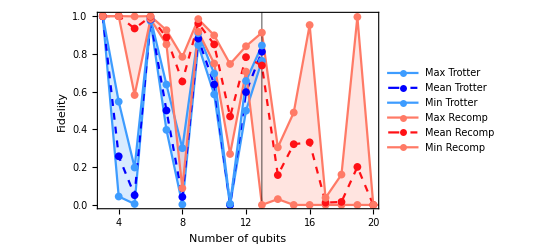

```mathematica
ListLinePlot[
	timify /@ {
	trotmin,trotmean,trotmax,
	recmin,recmean,recmax},
	FrameLabel->{
	{"Fidelity", Null},{"Number of qubits", 
	"Performance over 20 Ising Hamiltonians"}},
	PlotStyle-> {
		RGBColor[0.238758, 0.610466, 1.],Directive[Blue,Dashed], RGBColor[0.238758, 0.610466, 1.],
		RGBColor[1., 0.4770567658488352, 0.3999994395810451],Directive[RGBColor[1., 0.06811595600706821, 0.0851449450088353],Dashed],RGBColor[1., 0.4770567658488352, 0.3999994395810451]},
	GridLines->{{2+Length[trotterdata]},{}},
	GridLinesStyle->Black,
	Filling->{1->{3}, 4->{6}},
	PlotRange->{{3,20}, {0,1}},
	PlotMarkers->{●, 8},
	LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->12},
	Frame->True, FrameStyle->Black, 
	FrameTicks->{{Automatic,None},{Automatic,None}},
	PlotLegends-> {
		"Max Trotter","Mean Trotter", "Min Trotter\n",
		"Max Recomp", "Mean Recomp", "Min Recomp"}
]
```

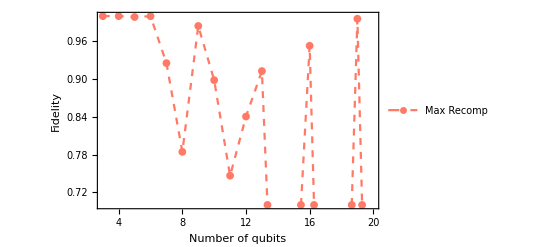

```mathematica
ListLinePlot[
	timify @ recmax,
	FrameLabel->{
	{"Fidelity", Null},{"Number of qubits", 
	"Performance over 20 Ising Hamiltonians"}},
	PlotStyle-> {
		RGBColor[1., 0.4770567658488352, 0.3999994395810451],Directive[RGBColor[1., 0.06811595600706821, 0.0851449450088353],Dashed],RGBColor[1., 0.4770567658488352, 0.3999994395810451]},
	PlotRange->{{3,20}, {0.7,1}},
	PlotMarkers->{●, 8},
	LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->12},
	Frame->True, FrameStyle->Black, 
	FrameTicks->{{Automatic,None},{Automatic,None}},
	PlotLegends-> {"Max Recomp"}
]
```

## Squeezed State results (fixed iter)

```mathematica
{sqzmean,sqzdev, sqzmax} = {Mean /@ #, StandardDeviation /@ #, Max /@ #}& @ Get["recomp_squeezed_from_3.txt"]["recompfids"];
qubify[series_] :=
	Transpose[{Range[3,2+Length[series]], series}]
```

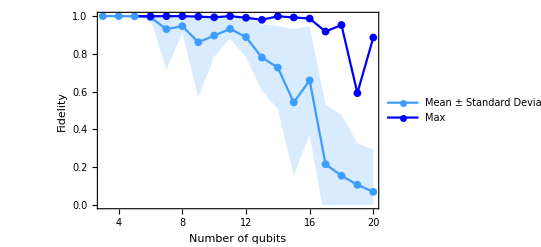

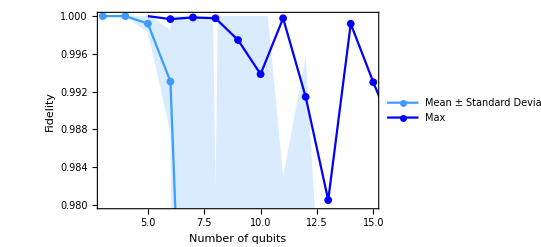

```mathematica
ListLinePlot[
	qubify /@ {sqzmean-sqzdev, sqzmean+sqzdev, sqzmean,sqzmax},

	FrameLabel->{
	{"Fidelity", Null},{"Number of qubits", 
	"Performance over 20 random squeezed states"}},
	PlotStyle-> {Directive[RGBColor[0.49250533333333335, 0.7403106666666666, 1.],Opacity[0]],Directive[RGBColor[0.49250533333333335, 0.7403106666666666, 1.],Opacity[0]], RGBColor[0.238758, 0.610466, 1.], Directive[Blue], RGBColor[0.238758, 0.610466, 1.]},
	Filling -> {3->{1}, 3->{2}},
	PlotRange->{{3,20}, {0,1}},
	PlotMarkers->{●, 8},
	LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->12},
	Frame->True, FrameStyle->Black, 
	FrameTicks->{{Automatic,None},{Automatic,None}},
	PlotLegends-> {None,None,"Mean ± Standard Deviation", "Max"}
]

Show[%, PlotRange -> {{3,15},{.98,1}}]
```

## Squeezed State results (converge-abort)

```mathematica
results = Get["recomp_convergeabort_squeezed_from_3.txt"];
```

Iterations to converge

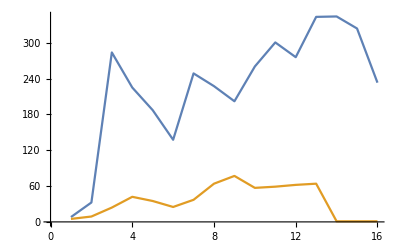

```mathematica
{itermeans,itersdev, itersmin} = N @ {Mean /@ #, StandardDeviation /@ #, Min /@ #}& @ Table[
	Length /@ results["fidlogs"][[n]],
	{n,1,Length @ results @ "fidlogs"}
];
ListLinePlot[
	{itermeans, itersmin}
]
```

Number converging to within fidelity threshold

```mathematica
convs = Table[Select[results["fidlogs"][[t]], (Length[#]<499&)], {t,Length@results@"fidlogs"}];
goodconvs = Table[Select[convs[[t]], (Last[#]≥.99&)], {t,Length@convs}];
```

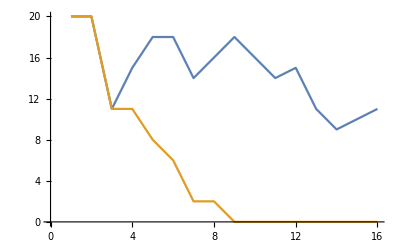

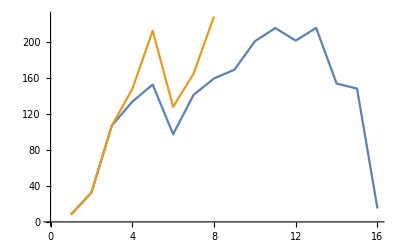

```mathematica
ListLinePlot[{Length /@ convs, Length /@ goodconvs}]
ListLinePlot[
	{Mean /@ Table[ Length /@ convs[[n]], {n,Length@goodconvs}],
	Mean /@ Table[ Length /@ goodconvs[[n]], {n,Length@goodconvs}]}
]
```

```mathematica
Manipulate[
ListLinePlot[
	goodconvs[[n]],
	GridLines->{{},{.99}},
	GridLinesStyle->Directive[Black,Thick]
], 
{n,1,Length @ goodconvs,1}
]
```